This notebook is the model that powers https://covidmodelingproject.com/. It builds upon earlier work from Harvard https://github.com/c2-d2/npi.

Initialize best-guess parameter values, and import raw data

```mathematica
(* Formatting *)
dateticks={{0,Rotate["Jan",π/2]},{0,Text[Style["\n\n2020",FontSize->14]]},{(31),""},{(31+28),""},{(31+28+31),Rotate["Apr",π/2]},{(31+28+31+30),""},{(31+28+31+30+31),""},{(31+28+31+30+31+30),Rotate["July",π/2]},{(31+28+31+30+31+30+31),""},{(31+28+31+30+31+30+31+31),""},{(31+28+31+30+31+30+31+31+30),Rotate["Oct",π/2]},{(31+28+31+30+31+30+31+31+30+31),""},{(31+28+31+30+31+30+31+31+30+31+30),""},{365,Rotate["Jan",π/2]},{365,Text[Style["\n\n2021",FontSize->14]]},{365+(31),""},{365+(31+28),""},{365+(31+28+31),Rotate["Apr",π/2]},{365+(31+28+31+30),""},{365+(31+28+31+30+31),""},{365+(31+28+31+30+31+30),Rotate["July",π/2]},{365+(31+28+31+30+31+30+31),""},{365+(31+28+31+30+31+30+31+31),""},{365+(31+28+31+30+31+30+31+31+30),Rotate["Oct",π/2]},{365+(31+28+31+30+31+30+31+31+30+31),""},{365+(31+28+31+30+31+30+31+31+30+31+30),""},{365*2,Rotate["Jan",π/2]},{365*2,Text[Style["\n\n2022",FontSize->14]]},{365*2+(31),""},{365*2+(31+28),""},{365*2+(31+28+31),Rotate["Apr",π/2]},{365*2+(31+28+31+30),""},{365*2+(31+28+31+30+31),""},{365*2+(31+28+31+30+31+30),Rotate["July",π/2]},{365*2+(31+28+31+30+31+30+31),""},{365*2+(31+28+31+30+31+30+31+31),""},{365*2+(31+28+31+30+31+30+31+31+30),Rotate["Oct",π/2]}};

(* some basic national data from covidtracking.com *)
USAActuals={{58,15},{59,15},{60,19},{61,24},{62,42},{63,57},{64,85},{65,111},{66,175},{67,252},{68,353},{69,497},{70,645},{71,936},{72,1205},{73,1598},{74,2163},{75,2825},{76,3501},{77,4373},{78,5662},{79,8074},{80,12018},{81,17438},{82,23710},{83,32341},{84,42752}};
USADeaths={{61,1},{62,2},{63,6},{64,9},{65,11},{66,11},{67,14},{68,19},{69,21},{70,26},{71,31},{72,37},{73,41},{74,49},{75,56},{76,62},{77,75},{78,96},{79,122},{80,174},{81,229},{82,296},{83,405},{84,516}};
USAPopulation=(327.2*10^6);

(* state data *)
ventalators=Association[{"AL"->920,"AK"->104,"AZ"->1309,"AR"->633,"CA"->6589,"CO"->913,"CT"->688,"DE"->200,"FL"->4307,"GA"->2093,"HI"->241,"ID"->182,"IL"->2311,"IN"->1472,"IA"->542,"KS"->514,"KY"->949,"LA"->1109,"ME"->214,"MD"->953,"MA"->1408,"MI"->1847,"MN"->811,"MS"->769,"MO"->1437,"MT"->158,"NE"->466,"NV"->753,"NH"->207,"NJ"->1487,"NM"->366,"NY"->4506,"NC"->1782,"ND"->180,"OH"->2729,"OK"->740,"OR"->503,"PA"->3013,"RI"->196,"SC"->949,"SD"->149,"TN"->1517,"TX"->5419,"UT"->503,"VT"->90,"VA"->1334,"WA"->836,"WV"->550,"WI"->864,"WY"->117}];

(* italy data *)
italyData=AssociationThread[ToString/@{"day","positive","death"}->#]&/@ImportString["52\t20\t1
53\t79\t2
54\t150\t3
55\t229\t6
56\t322\t10
57\t445\t12
58\t650\t17
59\t888\t21
60\t1128\t29
61\t1694\t34
62\t2036\t52
63\t2502\t79
64\t3089\t107
65\t3858\t148
66\t4636\t197
67\t5883\t233
68\t7375\t266
69\t9172\t463
70\t10149\t631
71\t12462\t827
72\t15133\t1016
73\t17600\t1266
74\t21157\t1441
75\t24747\t1809
76\t27980\t2158
77\t31506\t2503
78\t35713\t2978
79\t41035\t3405
80\t47021\t4032
81\t53578\t4825
82\t59138\t5475
83\t63927\t6077
84\t69176\t6820","TSV"];
ItalyPopulation=60.48*10^6;

franceData=AssociationThread[ToString/@{"day","positive","death"}->#]&/@ImportString["55\t12\t1
56\t18\t1
57\t38\t1
58\t57\t1
59\t100\t1
60\t130\t2
61\t191\t2
62\t212\t4
63\t285\t4
64\t423\t7
65\t613\t9
66\t949\t16
67\t1126\t21
68\t1421\t25
69\t1784\t33
70\t2281\t48
71\t2876\t61
72\t3661\t75
73\t4499\t91
74\t5423\t127
75\t6633\t148
76\t7730\t175
77\t9134\t244
78\t10995\t372
79\t12612\t450
80\t14459\t562
81\t16689\t674
82\t19856\t860
83\t22302\t1100
84\t25233\t1331","TSV"];
FrancePopulation = 66.99*10^6;

spainData=AssociationThread[ToString/@{"day","positive","death"}->#]&/@ImportString["54\t4\t1
55\t10\t1
56\t14\t1
57\t26\t1
58\t34\t1
59\t59\t1
60\t85\t1
61\t121\t1
62\t166\t2
63\t228\t2
64\t282\t3
65\t401\t8
66\t525\t10
67\t674\t17
68\t1231\t30
69\t1695\t26
70\t2277\t55
71\t3146\t86
72\t5232\t133
73\t6391\t196
74\t7988\t294
75\t9942\t342
76\t11826\t533
77\t14769\t638
78\t18077\t833
79\t21571\t1093
80\t25496\t1381
81\t29909\t1813
82\t35480\t2342
83\t42058\t2994
84\t49515\t3647","TSV"];
SpainPopulation=46.66*10^6;

stateDistancingData=AssociationThread[ToString/@{"state","baseline","d69","d70","d71","d72","d73","d74","d75","d76","d77","d78","d79","d80","d81"}->#]&/@ImportString["AZ\t100\t100\t100\t99\t99\t100\t100\t100\t96\t81\t80\t73\t66\t64
CA\t90\t90\t90\t90\t90\t72.9\t72.9\t73.8\t74.7\t69.3\t63\t54.9\t46.8\t46.8
CO\t90\t90\t90\t90\t90\t89.1\t89.1\t87.3\t79.2\t72\t52.2\t54.9\t53.1\t56.7
CT\t110\t108.9\t108.9\t104.5\t104.5\t85.8\t85.8\t91.3\t85.8\t82.5\t74.8\t68.2\t59.4\t59.4
FL\t80\t80\t80\t80\t80\t80\t80\t77.6\t75.2\t70.4\t64\t58.4\t48.8\t46.4
GA\t90\t90\t90\t90\t90\t79.2\t79.2\t85.5\t81\t79.2\t75.6\t64.8\t57.6\t57.6
IL\t100\t100\t100\t100\t100\t85\t85\t90\t88\t82\t77\t71\t60\t53
IN\t100\t100\t100\t100\t100\t80\t80\t96\t93\t94\t88\t78\t66\t66
LA\t100\t100\t100\t100\t100\t86\t86\t91\t85\t83\t78\t63\t55\t61
MA\t110\t108.9\t108.9\t103.4\t103.4\t90.2\t90.2\t90.2\t77\t71.5\t69.3\t63.8\t58.3\t55
MI\t130\t130\t130\t126.1\t126.1\t100.1\t100.1\t111.8\t106.6\t107.9\t96.2\t83.2\t71.5\t75.4
NJ\t120\t120\t120\t111.6\t111.6\t98.4\t98.4\t96\t86.4\t82.8\t76.8\t70.8\t60\t54
NY\t125\t122.5\t122.5\t122.5\t122.5\t103.75\t103.75\t103.75\t96.25\t92.5\t85\t76.25\t65\t63.75
OH\t110\t110\t110\t110\t110\t89.1\t89.1\t95.7\t97.9\t94.6\t89.1\t75.9\t66\t68.2
OR\t90\t89.1\t89.1\t83.7\t83.7\t72.9\t72.9\t84.6\t79.2\t77.4\t75.6\t72\t67.5\t63.9
PA\t110\t110\t110\t110\t110\t92.4\t92.4\t100.1\t92.4\t90.2\t85.8\t71.5\t60.5\t63.8
SC\t100\t100\t100\t100\t100\t94\t94\t100\t96\t90\t88\t75\t66\t63
TX\t90\t90\t90\t90\t90\t82.8\t82.8\t86.4\t81.9\t78.3\t70.2\t58.5\t51.3\t54.9
VA\t90\t90\t90\t90\t90\t79.2\t79.2\t81.9\t79.2\t74.7\t70.2\t62.1\t55.8\t57.6
VT\t110\t103.4\t103.4\t110\t110\t99\t99\t97.9\t89.1\t90.2\t81.4\t59.4\t59.4\t53.9
WA\t80\t74.4\t74.4\t72\t72\t63.2\t63.2\t69.6\t64.8\t60.8\t59.2\t56.8\t51.2\t51.2
WI\t110\t110\t110\t110\t110\t93.5\t93.5\t92.4\t99\t92.4\t86.9\t74.8\t66\t68.2","TSV"];


containedText=Text[Framed[Style["Virus Contained",FontSize->24,Bold,Black,FontFamily->"Calibri"],Background->Green,ContentPadding->False]];
containedGraphics=Graphics[containedText,ImageSize->Rasterize[containedText,"RasterSize"]];
heardText=Text[Framed[Style["Herd Immunity Developed",FontSize->24,Bold,Black,FontFamily->"Calibri"],Background->Red,ContentPadding->False]];
heardGraphics=Graphics[heardText,ImageSize->Rasterize[heardText,"RasterSize"]];
icuBelowCapacity=Text[Framed[Style["ICU Below Capacity",FontSize->24,Bold,Black,FontFamily->"Calibri"],Background->Green,ContentPadding->False]];
icuBelowCapacityGraphics=Graphics[icuBelowCapacity,ImageSize->Rasterize[icuBelowCapacity,"RasterSize"]];
icuOvershotText=Text[Framed[Style["ICU Capacity Overshot",FontSize->24,Bold,Black,FontFamily->"Calibri"],Background->Red,ContentPadding->False]];
icuOvershotTextGraphics=Graphics[icuOvershotText,ImageSize->Rasterize[icuOvershotText,"RasterSize"]];


(* These represent our best-guess parameters for the disease spread model,some of them vary by state and are gathered/computed later in that case.Otherwise these represent best-guessees derived from US/Italy national data on COVID-19 deaths. *)
(* demographic indep parameters *)
daysFromInfectedToInfectious0 = 2.8; (*Rate of progressing to infectiousness, days*)
daysUntilNotInfectiousOrHospitalized0 = 2.5; (*Rate of losing infectiousness or going to the hospital, weeks*)
daysToLeaveHosptialNonCritical0 = 8; (*Rate of leaving hospital for those not going to critical care, weeks*)
daysTogoToCriticalCare0 = 6; (*Rate of leaving hospital and going to critical care, weeks*)
daysFromCriticalToRecoveredOrDeceased0 = 3.2; (*Rate of leaving critical care, weeks*)
pPCRH0=0.114;
pPCRNH0=0.08;
 
(* virus start parameters *)
 initalInfectionImpulse0=12.5;
importlength = 3; (*Duration of pulse in force of infection for establishment, days*)

importtime = (31+20);  (*Establishment time, N days before X Cases*)

(* mitigation parameters *)
r0natural0 = 3.1; 

(* demographic dependent transition probabilities *)
(*pHospitalized=0.10;
pCriticalGivenHospitalized=0.3;
pC = pCriticalGivenHospitalized*pHospitalized; (*Probability of needing critical care*)
pH = (1-pCriticalGivenHospitalized)*pHospitalized; (*Probability of hospitalization but not critical care*)
pS = 1-(pC + pH); (*Probability of not needing care*)*)

fractionOfCriticalDeceased0= 0.3;(*Fraction of critical patents who pass *)
containmentThresholdRatio0 = 100/USAPopulation;

(* model predict max *)
tmax = 5*365;

medianHospitalizationAge0=65;
ageCriticalDependence0=3; (* interpret as: steepness of age depencence*)
ageHospitalizedDependence0=5; (* interpret as: steepness of age depencence*)
pHospitalized100Yo=0.25;
pCriticalGivenHospitalized100Yo=0.4;
pC0 = pCriticalGivenHospitalized100Yo*pHospitalized100Yo; (*Probability of needing critical care*)
pH0 = (1-pCriticalGivenHospitalized100Yo)*pHospitalized100Yo; (*Probability of hospitalization but not critical care*)
pS0 = 1-(pC0 + pH0); (*Probability of not needing care*)
```

Placeholder for figuring out better TSV -> Piecewise function parsing logic (to run this remove the semicolon and then copy the contents in the CopyAs menu and paste below in the stateHistoricalDistancing)

```mathematica
stateHistoryHelper=StringTemplate["\"`state`\"-><|\"scenario1\"->{{`baseline`/100,t<69},{`d69`/100,69<=t<70},{`d70`/100,70<=t<71},{`d71`/100,71<=t<72},{`d72`/100,72<=t<73},{`d73`/100,73<=t<74},{`d74`/100,74<=t<75},{`d75`/100,75<=t<76},{`d76`/100,76<=t<77},{`d77`/100,77<=t<78},{`d78`/100,78<=t<79},{`d79`/100,79<=t<80},{`d80`/100,80<=t<81},{`d81`/100,81<=t<82},{`d80`/100,82<=t<175},{`baseline`/100,175<=t<=tmax}},
\"scenario2\"->{{`baseline`/100,t<69},{`d69`/100,t<=69},{`d70`/100,70<=t<71},{`d71`/100,71<=t<72},{`d72`/100,72<=t<73},{`d73`/100,73<=t<74},{`d74`/100,74<=t<75},{`d75`/100,75<=t<76},{`d76`/100,76<=t<77},{`d77`/100,77<=t<78},{`d78`/100,78<=t<79},{`d79`/100,79<=t<80},{`d80`/100,80<=t<81},{`d81`/100,81<=t<82},{40/100,82<=t<175},{`baseline`/100,175<=t<=tmax}},
\"scenario3\"->{{`baseline`/100,t<69},{`d69`/100,t<=69},{`d70`/100,70<=t<71},{`d71`/100,71<=t<72},{`d72`/100,72<=t<73},{`d73`/100,73<=t<74},{`d74`/100,74<=t<75},{`d75`/100,75<=t<76},{`d76`/100,76<=t<77},{`d77`/100,77<=t<78},{`d78`/100,78<=t<79},{`d79`/100,79<=t<80},{`d80`/100,80<=t<81},{`d81`/100,81<=t<82},{11/100,82<=t<145},{`baseline`/100,145<=t<=tmax}},
\"scenario4\"->{{`baseline`/100,t<69},{`d69`/100,t<=69},{`d70`/100,70<=t<71},{`d71`/100,71<=t<72},{`d72`/100,72<=t<73},{`d73`/100,73<=t<74},{`d74`/100,74<=t<75},{`d75`/100,75<=t<76},{`d76`/100,76<=t<77},{`d77`/100,77<=t<78},{`d78`/100,78<=t<79},{`d79`/100,79<=t<80},{`d80`/100,80<=t<81},{`d81`/100,81<=t<82},{`baseline`/100,82<=t<=tmax}}|>"][#]&/@stateDistancingData;
```

```mathematica
today=QuantityMagnitude[DateDifference[DateList[{2020,1,1}],Today]];
distancingStates={"CA","CO","CT","FL","GA","IL","IN","LA","MA","MI","NJ","NY","OH","OR","PA","SC","TX","VA","VT","WA","WI"};
stateHistoricalDistancing[state_,scenario_,t_]:=Association[{"AZ"-><|"scenario1"->{{100/100,t<69},{100/100,69≤t<70},{100/100,70≤t<71},{99/100,71≤t<72},{99/100,72≤t<73},{100/100,73≤t<74},{100/100,74≤t<75},{100/100,75≤t<76},{96/100,76≤t<77},{81/100,77≤t<78},{80/100,78≤t<79},{73/100,79≤t<80},{66/100,80≤t<81},{64/100,81≤t<82},{66/100,82≤t<175},{100/100,175≤t≤tmax}},"scenario2"->{{100/100,t<69},{100/100,t≤69},{100/100,70≤t<71},{99/100,71≤t<72},{99/100,72≤t<73},{100/100,73≤t<74},{100/100,74≤t<75},{100/100,75≤t<76},{96/100,76≤t<77},{81/100,77≤t<78},{80/100,78≤t<79},{73/100,79≤t<80},{66/100,80≤t<81},{64/100,81≤t<82},{40/100,82≤t<175},{100/100,175≤t≤tmax}},"scenario3"->{{100/100,t<69},{100/100,t≤69},{100/100,70≤t<71},{99/100,71≤t<72},{99/100,72≤t<73},{100/100,73≤t<74},{100/100,74≤t<75},{100/100,75≤t<76},{96/100,76≤t<77},{81/100,77≤t<78},{80/100,78≤t<79},{73/100,79≤t<80},{66/100,80≤t<81},{64/100,81≤t<82},{11/100,82≤t<145},{100/100,145≤t≤tmax}},"scenario4"->{{100/100,t<69},{100/100,t≤69},{100/100,70≤t<71},{99/100,71≤t<72},{99/100,72≤t<73},{100/100,73≤t<74},{100/100,74≤t<75},{100/100,75≤t<76},{96/100,76≤t<77},{81/100,77≤t<78},{80/100,78≤t<79},{73/100,79≤t<80},{66/100,80≤t<81},{64/100,81≤t<82},{100/100,82≤t≤tmax}}|>,"CA"-><|"scenario1"->{{90/100,t<69},{90/100,69≤t<70},{90/100,70≤t<71},{90/100,71≤t<72},{90/100,72≤t<73},{72.9/100,73≤t<74},{72.9/100,74≤t<75},{73.8/100,75≤t<76},{74.7/100,76≤t<77},{69.3/100,77≤t<78},{63/100,78≤t<79},{54.9/100,79≤t<80},{46.8/100,80≤t<81},{46.8/100,81≤t<82},{46.8/100,82≤t<175},{90/100,175≤t≤tmax}},"scenario2"->{{90/100,t<69},{90/100,t≤69},{90/100,70≤t<71},{90/100,71≤t<72},{90/100,72≤t<73},{72.9/100,73≤t<74},{72.9/100,74≤t<75},{73.8/100,75≤t<76},{74.7/100,76≤t<77},{69.3/100,77≤t<78},{63/100,78≤t<79},{54.9/100,79≤t<80},{46.8/100,80≤t<81},{46.8/100,81≤t<82},{40/100,82≤t<175},{90/100,175≤t≤tmax}},"scenario3"->{{90/100,t<69},{90/100,t≤69},{90/100,70≤t<71},{90/100,71≤t<72},{90/100,72≤t<73},{72.9/100,73≤t<74},{72.9/100,74≤t<75},{73.8/100,75≤t<76},{74.7/100,76≤t<77},{69.3/100,77≤t<78},{63/100,78≤t<79},{54.9/100,79≤t<80},{46.8/100,80≤t<81},{46.8/100,81≤t<82},{11/100,82≤t<145},{90/100,145≤t≤tmax}},"scenario4"->{{90/100,t<69},{90/100,t≤69},{90/100,70≤t<71},{90/100,71≤t<72},{90/100,72≤t<73},{72.9/100,73≤t<74},{72.9/100,74≤t<75},{73.8/100,75≤t<76},{74.7/100,76≤t<77},{69.3/100,77≤t<78},{63/100,78≤t<79},{54.9/100,79≤t<80},{46.8/100,80≤t<81},{46.8/100,81≤t<82},{90/100,82≤t≤tmax}}|>,"CO"-><|"scenario1"->{{90/100,t<69},{90/100,69≤t<70},{90/100,70≤t<71},{90/100,71≤t<72},{90/100,72≤t<73},{89.1/100,73≤t<74},{89.1/100,74≤t<75},{87.3/100,75≤t<76},{79.2/100,76≤t<77},{72/100,77≤t<78},{52.2/100,78≤t<79},{54.9/100,79≤t<80},{53.1/100,80≤t<81},{56.7/100,81≤t<82},{53.1/100,82≤t<175},{90/100,175≤t≤tmax}},"scenario2"->{{90/100,t<69},{90/100,t≤69},{90/100,70≤t<71},{90/100,71≤t<72},{90/100,72≤t<73},{89.1/100,73≤t<74},{89.1/100,74≤t<75},{87.3/100,75≤t<76},{79.2/100,76≤t<77},{72/100,77≤t<78},{52.2/100,78≤t<79},{54.9/100,79≤t<80},{53.1/100,80≤t<81},{56.7/100,81≤t<82},{40/100,82≤t<175},{90/100,175≤t≤tmax}},"scenario3"->{{90/100,t<69},{90/100,t≤69},{90/100,70≤t<71},{90/100,71≤t<72},{90/100,72≤t<73},{89.1/100,73≤t<74},{89.1/100,74≤t<75},{87.3/100,75≤t<76},{79.2/100,76≤t<77},{72/100,77≤t<78},{52.2/100,78≤t<79},{54.9/100,79≤t<80},{53.1/100,80≤t<81},{56.7/100,81≤t<82},{11/100,82≤t<145},{90/100,145≤t≤tmax}},"scenario4"->{{90/100,t<69},{90/100,t≤69},{90/100,70≤t<71},{90/100,71≤t<72},{90/100,72≤t<73},{89.1/100,73≤t<74},{89.1/100,74≤t<75},{87.3/100,75≤t<76},{79.2/100,76≤t<77},{72/100,77≤t<78},{52.2/100,78≤t<79},{54.9/100,79≤t<80},{53.1/100,80≤t<81},{56.7/100,81≤t<82},{90/100,82≤t≤tmax}}|>,"CT"-><|"scenario1"->{{110/100,t<69},{108.9/100,69≤t<70},{108.9/100,70≤t<71},{104.5/100,71≤t<72},{104.5/100,72≤t<73},{85.8/100,73≤t<74},{85.8/100,74≤t<75},{91.3/100,75≤t<76},{85.8/100,76≤t<77},{82.5/100,77≤t<78},{74.8/100,78≤t<79},{68.2/100,79≤t<80},{59.4/100,80≤t<81},{59.4/100,81≤t<82},{59.4/100,82≤t<175},{110/100,175≤t≤tmax}},"scenario2"->{{110/100,t<69},{108.9/100,t≤69},{108.9/100,70≤t<71},{104.5/100,71≤t<72},{104.5/100,72≤t<73},{85.8/100,73≤t<74},{85.8/100,74≤t<75},{91.3/100,75≤t<76},{85.8/100,76≤t<77},{82.5/100,77≤t<78},{74.8/100,78≤t<79},{68.2/100,79≤t<80},{59.4/100,80≤t<81},{59.4/100,81≤t<82},{40/100,82≤t<175},{110/100,175≤t≤tmax}},"scenario3"->{{110/100,t<69},{108.9/100,t≤69},{108.9/100,70≤t<71},{104.5/100,71≤t<72},{104.5/100,72≤t<73},{85.8/100,73≤t<74},{85.8/100,74≤t<75},{91.3/100,75≤t<76},{85.8/100,76≤t<77},{82.5/100,77≤t<78},{74.8/100,78≤t<79},{68.2/100,79≤t<80},{59.4/100,80≤t<81},{59.4/100,81≤t<82},{11/100,82≤t<145},{110/100,145≤t≤tmax}},"scenario4"->{{110/100,t<69},{108.9/100,t≤69},{108.9/100,70≤t<71},{104.5/100,71≤t<72},{104.5/100,72≤t<73},{85.8/100,73≤t<74},{85.8/100,74≤t<75},{91.3/100,75≤t<76},{85.8/100,76≤t<77},{82.5/100,77≤t<78},{74.8/100,78≤t<79},{68.2/100,79≤t<80},{59.4/100,80≤t<81},{59.4/100,81≤t<82},{110/100,82≤t≤tmax}}|>,"FL"-><|"scenario1"->{{80/100,t<69},{80/100,69≤t<70},{80/100,70≤t<71},{80/100,71≤t<72},{80/100,72≤t<73},{80/100,73≤t<74},{80/100,74≤t<75},{77.6/100,75≤t<76},{75.2/100,76≤t<77},{70.4/100,77≤t<78},{64/100,78≤t<79},{58.4/100,79≤t<80},{48.8/100,80≤t<81},{46.4/100,81≤t<82},{48.8/100,82≤t<175},{80/100,175≤t≤tmax}},"scenario2"->{{80/100,t<69},{80/100,t≤69},{80/100,70≤t<71},{80/100,71≤t<72},{80/100,72≤t<73},{80/100,73≤t<74},{80/100,74≤t<75},{77.6/100,75≤t<76},{75.2/100,76≤t<77},{70.4/100,77≤t<78},{64/100,78≤t<79},{58.4/100,79≤t<80},{48.8/100,80≤t<81},{46.4/100,81≤t<82},{40/100,82≤t<175},{80/100,175≤t≤tmax}},"scenario3"->{{80/100,t<69},{80/100,t≤69},{80/100,70≤t<71},{80/100,71≤t<72},{80/100,72≤t<73},{80/100,73≤t<74},{80/100,74≤t<75},{77.6/100,75≤t<76},{75.2/100,76≤t<77},{70.4/100,77≤t<78},{64/100,78≤t<79},{58.4/100,79≤t<80},{48.8/100,80≤t<81},{46.4/100,81≤t<82},{11/100,82≤t<145},{80/100,145≤t≤tmax}},"scenario4"->{{80/100,t<69},{80/100,t≤69},{80/100,70≤t<71},{80/100,71≤t<72},{80/100,72≤t<73},{80/100,73≤t<74},{80/100,74≤t<75},{77.6/100,75≤t<76},{75.2/100,76≤t<77},{70.4/100,77≤t<78},{64/100,78≤t<79},{58.4/100,79≤t<80},{48.8/100,80≤t<81},{46.4/100,81≤t<82},{80/100,82≤t≤tmax}}|>,"GA"-><|"scenario1"->{{90/100,t<69},{90/100,69≤t<70},{90/100,70≤t<71},{90/100,71≤t<72},{90/100,72≤t<73},{79.2/100,73≤t<74},{79.2/100,74≤t<75},{85.5/100,75≤t<76},{81/100,76≤t<77},{79.2/100,77≤t<78},{75.6/100,78≤t<79},{64.8/100,79≤t<80},{57.6/100,80≤t<81},{57.6/100,81≤t<82},{57.6/100,82≤t<175},{90/100,175≤t≤tmax}},"scenario2"->{{90/100,t<69},{90/100,t≤69},{90/100,70≤t<71},{90/100,71≤t<72},{90/100,72≤t<73},{79.2/100,73≤t<74},{79.2/100,74≤t<75},{85.5/100,75≤t<76},{81/100,76≤t<77},{79.2/100,77≤t<78},{75.6/100,78≤t<79},{64.8/100,79≤t<80},{57.6/100,80≤t<81},{57.6/100,81≤t<82},{40/100,82≤t<175},{90/100,175≤t≤tmax}},"scenario3"->{{90/100,t<69},{90/100,t≤69},{90/100,70≤t<71},{90/100,71≤t<72},{90/100,72≤t<73},{79.2/100,73≤t<74},{79.2/100,74≤t<75},{85.5/100,75≤t<76},{81/100,76≤t<77},{79.2/100,77≤t<78},{75.6/100,78≤t<79},{64.8/100,79≤t<80},{57.6/100,80≤t<81},{57.6/100,81≤t<82},{11/100,82≤t<145},{90/100,145≤t≤tmax}},"scenario4"->{{90/100,t<69},{90/100,t≤69},{90/100,70≤t<71},{90/100,71≤t<72},{90/100,72≤t<73},{79.2/100,73≤t<74},{79.2/100,74≤t<75},{85.5/100,75≤t<76},{81/100,76≤t<77},{79.2/100,77≤t<78},{75.6/100,78≤t<79},{64.8/100,79≤t<80},{57.6/100,80≤t<81},{57.6/100,81≤t<82},{90/100,82≤t≤tmax}}|>,"IL"-><|"scenario1"->{{100/100,t<69},{100/100,69≤t<70},{100/100,70≤t<71},{100/100,71≤t<72},{100/100,72≤t<73},{85/100,73≤t<74},{85/100,74≤t<75},{90/100,75≤t<76},{88/100,76≤t<77},{82/100,77≤t<78},{77/100,78≤t<79},{71/100,79≤t<80},{60/100,80≤t<81},{53/100,81≤t<82},{60/100,82≤t<175},{100/100,175≤t≤tmax}},"scenario2"->{{100/100,t<69},{100/100,t≤69},{100/100,70≤t<71},{100/100,71≤t<72},{100/100,72≤t<73},{85/100,73≤t<74},{85/100,74≤t<75},{90/100,75≤t<76},{88/100,76≤t<77},{82/100,77≤t<78},{77/100,78≤t<79},{71/100,79≤t<80},{60/100,80≤t<81},{53/100,81≤t<82},{40/100,82≤t<175},{100/100,175≤t≤tmax}},"scenario3"->{{100/100,t<69},{100/100,t≤69},{100/100,70≤t<71},{100/100,71≤t<72},{100/100,72≤t<73},{85/100,73≤t<74},{85/100,74≤t<75},{90/100,75≤t<76},{88/100,76≤t<77},{82/100,77≤t<78},{77/100,78≤t<79},{71/100,79≤t<80},{60/100,80≤t<81},{53/100,81≤t<82},{11/100,82≤t<145},{100/100,145≤t≤tmax}},"scenario4"->{{100/100,t<69},{100/100,t≤69},{100/100,70≤t<71},{100/100,71≤t<72},{100/100,72≤t<73},{85/100,73≤t<74},{85/100,74≤t<75},{90/100,75≤t<76},{88/100,76≤t<77},{82/100,77≤t<78},{77/100,78≤t<79},{71/100,79≤t<80},{60/100,80≤t<81},{53/100,81≤t<82},{100/100,82≤t≤tmax}}|>,"IN"-><|"scenario1"->{{100/100,t<69},{100/100,69≤t<70},{100/100,70≤t<71},{100/100,71≤t<72},{100/100,72≤t<73},{80/100,73≤t<74},{80/100,74≤t<75},{96/100,75≤t<76},{93/100,76≤t<77},{94/100,77≤t<78},{88/100,78≤t<79},{78/100,79≤t<80},{66/100,80≤t<81},{66/100,81≤t<82},{66/100,82≤t<175},{100/100,175≤t≤tmax}},"scenario2"->{{100/100,t<69},{100/100,t≤69},{100/100,70≤t<71},{100/100,71≤t<72},{100/100,72≤t<73},{80/100,73≤t<74},{80/100,74≤t<75},{96/100,75≤t<76},{93/100,76≤t<77},{94/100,77≤t<78},{88/100,78≤t<79},{78/100,79≤t<80},{66/100,80≤t<81},{66/100,81≤t<82},{40/100,82≤t<175},{100/100,175≤t≤tmax}},"scenario3"->{{100/100,t<69},{100/100,t≤69},{100/100,70≤t<71},{100/100,71≤t<72},{100/100,72≤t<73},{80/100,73≤t<74},{80/100,74≤t<75},{96/100,75≤t<76},{93/100,76≤t<77},{94/100,77≤t<78},{88/100,78≤t<79},{78/100,79≤t<80},{66/100,80≤t<81},{66/100,81≤t<82},{11/100,82≤t<145},{100/100,145≤t≤tmax}},"scenario4"->{{100/100,t<69},{100/100,t≤69},{100/100,70≤t<71},{100/100,71≤t<72},{100/100,72≤t<73},{80/100,73≤t<74},{80/100,74≤t<75},{96/100,75≤t<76},{93/100,76≤t<77},{94/100,77≤t<78},{88/100,78≤t<79},{78/100,79≤t<80},{66/100,80≤t<81},{66/100,81≤t<82},{100/100,82≤t≤tmax}}|>,"LA"-><|"scenario1"->{{100/100,t<69},{100/100,69≤t<70},{100/100,70≤t<71},{100/100,71≤t<72},{100/100,72≤t<73},{86/100,73≤t<74},{86/100,74≤t<75},{91/100,75≤t<76},{85/100,76≤t<77},{83/100,77≤t<78},{78/100,78≤t<79},{63/100,79≤t<80},{55/100,80≤t<81},{61/100,81≤t<82},{55/100,82≤t<175},{100/100,175≤t≤tmax}},"scenario2"->{{100/100,t<69},{100/100,t≤69},{100/100,70≤t<71},{100/100,71≤t<72},{100/100,72≤t<73},{86/100,73≤t<74},{86/100,74≤t<75},{91/100,75≤t<76},{85/100,76≤t<77},{83/100,77≤t<78},{78/100,78≤t<79},{63/100,79≤t<80},{55/100,80≤t<81},{61/100,81≤t<82},{40/100,82≤t<175},{100/100,175≤t≤tmax}},"scenario3"->{{100/100,t<69},{100/100,t≤69},{100/100,70≤t<71},{100/100,71≤t<72},{100/100,72≤t<73},{86/100,73≤t<74},{86/100,74≤t<75},{91/100,75≤t<76},{85/100,76≤t<77},{83/100,77≤t<78},{78/100,78≤t<79},{63/100,79≤t<80},{55/100,80≤t<81},{61/100,81≤t<82},{11/100,82≤t<145},{100/100,145≤t≤tmax}},"scenario4"->{{100/100,t<69},{100/100,t≤69},{100/100,70≤t<71},{100/100,71≤t<72},{100/100,72≤t<73},{86/100,73≤t<74},{86/100,74≤t<75},{91/100,75≤t<76},{85/100,76≤t<77},{83/100,77≤t<78},{78/100,78≤t<79},{63/100,79≤t<80},{55/100,80≤t<81},{61/100,81≤t<82},{100/100,82≤t≤tmax}}|>,"MA"-><|"scenario1"->{{110/100,t<69},{108.9/100,69≤t<70},{108.9/100,70≤t<71},{103.4/100,71≤t<72},{103.4/100,72≤t<73},{90.2/100,73≤t<74},{90.2/100,74≤t<75},{90.2/100,75≤t<76},{77/100,76≤t<77},{71.5/100,77≤t<78},{69.3/100,78≤t<79},{63.8/100,79≤t<80},{58.3/100,80≤t<81},{55/100,81≤t<82},{58.3/100,82≤t<175},{110/100,175≤t≤tmax}},"scenario2"->{{110/100,t<69},{108.9/100,t≤69},{108.9/100,70≤t<71},{103.4/100,71≤t<72},{103.4/100,72≤t<73},{90.2/100,73≤t<74},{90.2/100,74≤t<75},{90.2/100,75≤t<76},{77/100,76≤t<77},{71.5/100,77≤t<78},{69.3/100,78≤t<79},{63.8/100,79≤t<80},{58.3/100,80≤t<81},{55/100,81≤t<82},{40/100,82≤t<175},{110/100,175≤t≤tmax}},"scenario3"->{{110/100,t<69},{108.9/100,t≤69},{108.9/100,70≤t<71},{103.4/100,71≤t<72},{103.4/100,72≤t<73},{90.2/100,73≤t<74},{90.2/100,74≤t<75},{90.2/100,75≤t<76},{77/100,76≤t<77},{71.5/100,77≤t<78},{69.3/100,78≤t<79},{63.8/100,79≤t<80},{58.3/100,80≤t<81},{55/100,81≤t<82},{11/100,82≤t<145},{110/100,145≤t≤tmax}},"scenario4"->{{110/100,t<69},{108.9/100,t≤69},{108.9/100,70≤t<71},{103.4/100,71≤t<72},{103.4/100,72≤t<73},{90.2/100,73≤t<74},{90.2/100,74≤t<75},{90.2/100,75≤t<76},{77/100,76≤t<77},{71.5/100,77≤t<78},{69.3/100,78≤t<79},{63.8/100,79≤t<80},{58.3/100,80≤t<81},{55/100,81≤t<82},{110/100,82≤t≤tmax}}|>,"MI"-><|"scenario1"->{{130/100,t<69},{130/100,69≤t<70},{130/100,70≤t<71},{126.1/100,71≤t<72},{126.1/100,72≤t<73},{100.1/100,73≤t<74},{100.1/100,74≤t<75},{111.8/100,75≤t<76},{106.6/100,76≤t<77},{107.9/100,77≤t<78},{96.2/100,78≤t<79},{83.2/100,79≤t<80},{71.5/100,80≤t<81},{75.4/100,81≤t<82},{71.5/100,82≤t<175},{130/100,175≤t≤tmax}},"scenario2"->{{130/100,t<69},{130/100,t≤69},{130/100,70≤t<71},{126.1/100,71≤t<72},{126.1/100,72≤t<73},{100.1/100,73≤t<74},{100.1/100,74≤t<75},{111.8/100,75≤t<76},{106.6/100,76≤t<77},{107.9/100,77≤t<78},{96.2/100,78≤t<79},{83.2/100,79≤t<80},{71.5/100,80≤t<81},{75.4/100,81≤t<82},{40/100,82≤t<175},{130/100,175≤t≤tmax}},"scenario3"->{{130/100,t<69},{130/100,t≤69},{130/100,70≤t<71},{126.1/100,71≤t<72},{126.1/100,72≤t<73},{100.1/100,73≤t<74},{100.1/100,74≤t<75},{111.8/100,75≤t<76},{106.6/100,76≤t<77},{107.9/100,77≤t<78},{96.2/100,78≤t<79},{83.2/100,79≤t<80},{71.5/100,80≤t<81},{75.4/100,81≤t<82},{11/100,82≤t<145},{130/100,145≤t≤tmax}},"scenario4"->{{130/100,t<69},{130/100,t≤69},{130/100,70≤t<71},{126.1/100,71≤t<72},{126.1/100,72≤t<73},{100.1/100,73≤t<74},{100.1/100,74≤t<75},{111.8/100,75≤t<76},{106.6/100,76≤t<77},{107.9/100,77≤t<78},{96.2/100,78≤t<79},{83.2/100,79≤t<80},{71.5/100,80≤t<81},{75.4/100,81≤t<82},{130/100,82≤t≤tmax}}|>,"NJ"-><|"scenario1"->{{120/100,t<69},{120/100,69≤t<70},{120/100,70≤t<71},{111.6/100,71≤t<72},{111.6/100,72≤t<73},{98.4/100,73≤t<74},{98.4/100,74≤t<75},{96/100,75≤t<76},{86.4/100,76≤t<77},{82.8/100,77≤t<78},{76.8/100,78≤t<79},{70.8/100,79≤t<80},{60/100,80≤t<81},{54/100,81≤t<82},{60/100,82≤t<175},{120/100,175≤t≤tmax}},"scenario2"->{{120/100,t<69},{120/100,t≤69},{120/100,70≤t<71},{111.6/100,71≤t<72},{111.6/100,72≤t<73},{98.4/100,73≤t<74},{98.4/100,74≤t<75},{96/100,75≤t<76},{86.4/100,76≤t<77},{82.8/100,77≤t<78},{76.8/100,78≤t<79},{70.8/100,79≤t<80},{60/100,80≤t<81},{54/100,81≤t<82},{40/100,82≤t<175},{120/100,175≤t≤tmax}},"scenario3"->{{120/100,t<69},{120/100,t≤69},{120/100,70≤t<71},{111.6/100,71≤t<72},{111.6/100,72≤t<73},{98.4/100,73≤t<74},{98.4/100,74≤t<75},{96/100,75≤t<76},{86.4/100,76≤t<77},{82.8/100,77≤t<78},{76.8/100,78≤t<79},{70.8/100,79≤t<80},{60/100,80≤t<81},{54/100,81≤t<82},{11/100,82≤t<145},{120/100,145≤t≤tmax}},"scenario4"->{{120/100,t<69},{120/100,t≤69},{120/100,70≤t<71},{111.6/100,71≤t<72},{111.6/100,72≤t<73},{98.4/100,73≤t<74},{98.4/100,74≤t<75},{96/100,75≤t<76},{86.4/100,76≤t<77},{82.8/100,77≤t<78},{76.8/100,78≤t<79},{70.8/100,79≤t<80},{60/100,80≤t<81},{54/100,81≤t<82},{120/100,82≤t≤tmax}}|>,"NY"-><|"scenario1"->{{125/100,t<69},{122.5/100,69≤t<70},{122.5/100,70≤t<71},{122.5/100,71≤t<72},{122.5/100,72≤t<73},{103.75/100,73≤t<74},{103.75/100,74≤t<75},{103.75/100,75≤t<76},{96.25/100,76≤t<77},{92.5/100,77≤t<78},{85/100,78≤t<79},{76.25/100,79≤t<80},{65/100,80≤t<81},{63.75/100,81≤t<82},{65/100,82≤t<175},{125/100,175≤t≤tmax}},"scenario2"->{{125/100,t<69},{122.5/100,t≤69},{122.5/100,70≤t<71},{122.5/100,71≤t<72},{122.5/100,72≤t<73},{103.75/100,73≤t<74},{103.75/100,74≤t<75},{103.75/100,75≤t<76},{96.25/100,76≤t<77},{92.5/100,77≤t<78},{85/100,78≤t<79},{76.25/100,79≤t<80},{65/100,80≤t<81},{63.75/100,81≤t<82},{40/100,82≤t<175},{125/100,175≤t≤tmax}},"scenario3"->{{125/100,t<69},{122.5/100,t≤69},{122.5/100,70≤t<71},{122.5/100,71≤t<72},{122.5/100,72≤t<73},{103.75/100,73≤t<74},{103.75/100,74≤t<75},{103.75/100,75≤t<76},{96.25/100,76≤t<77},{92.5/100,77≤t<78},{85/100,78≤t<79},{76.25/100,79≤t<80},{65/100,80≤t<81},{63.75/100,81≤t<82},{11/100,82≤t<145},{125/100,145≤t≤tmax}},"scenario4"->{{125/100,t<69},{122.5/100,t≤69},{122.5/100,70≤t<71},{122.5/100,71≤t<72},{122.5/100,72≤t<73},{103.75/100,73≤t<74},{103.75/100,74≤t<75},{103.75/100,75≤t<76},{96.25/100,76≤t<77},{92.5/100,77≤t<78},{85/100,78≤t<79},{76.25/100,79≤t<80},{65/100,80≤t<81},{63.75/100,81≤t<82},{125/100,82≤t≤tmax}}|>,"OH"-><|"scenario1"->{{110/100,t<69},{110/100,69≤t<70},{110/100,70≤t<71},{110/100,71≤t<72},{110/100,72≤t<73},{89.1/100,73≤t<74},{89.1/100,74≤t<75},{95.7/100,75≤t<76},{97.9/100,76≤t<77},{94.6/100,77≤t<78},{89.1/100,78≤t<79},{75.9/100,79≤t<80},{66/100,80≤t<81},{68.2/100,81≤t<82},{66/100,82≤t<175},{110/100,175≤t≤tmax}},"scenario2"->{{110/100,t<69},{110/100,t≤69},{110/100,70≤t<71},{110/100,71≤t<72},{110/100,72≤t<73},{89.1/100,73≤t<74},{89.1/100,74≤t<75},{95.7/100,75≤t<76},{97.9/100,76≤t<77},{94.6/100,77≤t<78},{89.1/100,78≤t<79},{75.9/100,79≤t<80},{66/100,80≤t<81},{68.2/100,81≤t<82},{40/100,82≤t<175},{110/100,175≤t≤tmax}},"scenario3"->{{110/100,t<69},{110/100,t≤69},{110/100,70≤t<71},{110/100,71≤t<72},{110/100,72≤t<73},{89.1/100,73≤t<74},{89.1/100,74≤t<75},{95.7/100,75≤t<76},{97.9/100,76≤t<77},{94.6/100,77≤t<78},{89.1/100,78≤t<79},{75.9/100,79≤t<80},{66/100,80≤t<81},{68.2/100,81≤t<82},{11/100,82≤t<145},{110/100,145≤t≤tmax}},"scenario4"->{{110/100,t<69},{110/100,t≤69},{110/100,70≤t<71},{110/100,71≤t<72},{110/100,72≤t<73},{89.1/100,73≤t<74},{89.1/100,74≤t<75},{95.7/100,75≤t<76},{97.9/100,76≤t<77},{94.6/100,77≤t<78},{89.1/100,78≤t<79},{75.9/100,79≤t<80},{66/100,80≤t<81},{68.2/100,81≤t<82},{110/100,82≤t≤tmax}}|>,"OR"-><|"scenario1"->{{90/100,t<69},{89.1/100,69≤t<70},{89.1/100,70≤t<71},{83.7/100,71≤t<72},{83.7/100,72≤t<73},{72.9/100,73≤t<74},{72.9/100,74≤t<75},{84.6/100,75≤t<76},{79.2/100,76≤t<77},{77.4/100,77≤t<78},{75.6/100,78≤t<79},{72/100,79≤t<80},{67.5/100,80≤t<81},{63.9/100,81≤t<82},{67.5/100,82≤t<175},{90/100,175≤t≤tmax}},"scenario2"->{{90/100,t<69},{89.1/100,t≤69},{89.1/100,70≤t<71},{83.7/100,71≤t<72},{83.7/100,72≤t<73},{72.9/100,73≤t<74},{72.9/100,74≤t<75},{84.6/100,75≤t<76},{79.2/100,76≤t<77},{77.4/100,77≤t<78},{75.6/100,78≤t<79},{72/100,79≤t<80},{67.5/100,80≤t<81},{63.9/100,81≤t<82},{40/100,82≤t<175},{90/100,175≤t≤tmax}},"scenario3"->{{90/100,t<69},{89.1/100,t≤69},{89.1/100,70≤t<71},{83.7/100,71≤t<72},{83.7/100,72≤t<73},{72.9/100,73≤t<74},{72.9/100,74≤t<75},{84.6/100,75≤t<76},{79.2/100,76≤t<77},{77.4/100,77≤t<78},{75.6/100,78≤t<79},{72/100,79≤t<80},{67.5/100,80≤t<81},{63.9/100,81≤t<82},{11/100,82≤t<145},{90/100,145≤t≤tmax}},"scenario4"->{{90/100,t<69},{89.1/100,t≤69},{89.1/100,70≤t<71},{83.7/100,71≤t<72},{83.7/100,72≤t<73},{72.9/100,73≤t<74},{72.9/100,74≤t<75},{84.6/100,75≤t<76},{79.2/100,76≤t<77},{77.4/100,77≤t<78},{75.6/100,78≤t<79},{72/100,79≤t<80},{67.5/100,80≤t<81},{63.9/100,81≤t<82},{90/100,82≤t≤tmax}}|>,"PA"-><|"scenario1"->{{110/100,t<69},{110/100,69≤t<70},{110/100,70≤t<71},{110/100,71≤t<72},{110/100,72≤t<73},{92.4/100,73≤t<74},{92.4/100,74≤t<75},{100.1/100,75≤t<76},{92.4/100,76≤t<77},{90.2/100,77≤t<78},{85.8/100,78≤t<79},{71.5/100,79≤t<80},{60.5/100,80≤t<81},{63.8/100,81≤t<82},{60.5/100,82≤t<175},{110/100,175≤t≤tmax}},"scenario2"->{{110/100,t<69},{110/100,t≤69},{110/100,70≤t<71},{110/100,71≤t<72},{110/100,72≤t<73},{92.4/100,73≤t<74},{92.4/100,74≤t<75},{100.1/100,75≤t<76},{92.4/100,76≤t<77},{90.2/100,77≤t<78},{85.8/100,78≤t<79},{71.5/100,79≤t<80},{60.5/100,80≤t<81},{63.8/100,81≤t<82},{40/100,82≤t<175},{110/100,175≤t≤tmax}},"scenario3"->{{110/100,t<69},{110/100,t≤69},{110/100,70≤t<71},{110/100,71≤t<72},{110/100,72≤t<73},{92.4/100,73≤t<74},{92.4/100,74≤t<75},{100.1/100,75≤t<76},{92.4/100,76≤t<77},{90.2/100,77≤t<78},{85.8/100,78≤t<79},{71.5/100,79≤t<80},{60.5/100,80≤t<81},{63.8/100,81≤t<82},{11/100,82≤t<145},{110/100,145≤t≤tmax}},"scenario4"->{{110/100,t<69},{110/100,t≤69},{110/100,70≤t<71},{110/100,71≤t<72},{110/100,72≤t<73},{92.4/100,73≤t<74},{92.4/100,74≤t<75},{100.1/100,75≤t<76},{92.4/100,76≤t<77},{90.2/100,77≤t<78},{85.8/100,78≤t<79},{71.5/100,79≤t<80},{60.5/100,80≤t<81},{63.8/100,81≤t<82},{110/100,82≤t≤tmax}}|>,"SC"-><|"scenario1"->{{100/100,t<69},{100/100,69≤t<70},{100/100,70≤t<71},{100/100,71≤t<72},{100/100,72≤t<73},{94/100,73≤t<74},{94/100,74≤t<75},{100/100,75≤t<76},{96/100,76≤t<77},{90/100,77≤t<78},{88/100,78≤t<79},{75/100,79≤t<80},{66/100,80≤t<81},{63/100,81≤t<82},{66/100,82≤t<175},{100/100,175≤t≤tmax}},"scenario2"->{{100/100,t<69},{100/100,t≤69},{100/100,70≤t<71},{100/100,71≤t<72},{100/100,72≤t<73},{94/100,73≤t<74},{94/100,74≤t<75},{100/100,75≤t<76},{96/100,76≤t<77},{90/100,77≤t<78},{88/100,78≤t<79},{75/100,79≤t<80},{66/100,80≤t<81},{63/100,81≤t<82},{40/100,82≤t<175},{100/100,175≤t≤tmax}},"scenario3"->{{100/100,t<69},{100/100,t≤69},{100/100,70≤t<71},{100/100,71≤t<72},{100/100,72≤t<73},{94/100,73≤t<74},{94/100,74≤t<75},{100/100,75≤t<76},{96/100,76≤t<77},{90/100,77≤t<78},{88/100,78≤t<79},{75/100,79≤t<80},{66/100,80≤t<81},{63/100,81≤t<82},{11/100,82≤t<145},{100/100,145≤t≤tmax}},"scenario4"->{{100/100,t<69},{100/100,t≤69},{100/100,70≤t<71},{100/100,71≤t<72},{100/100,72≤t<73},{94/100,73≤t<74},{94/100,74≤t<75},{100/100,75≤t<76},{96/100,76≤t<77},{90/100,77≤t<78},{88/100,78≤t<79},{75/100,79≤t<80},{66/100,80≤t<81},{63/100,81≤t<82},{100/100,82≤t≤tmax}}|>,"TX"-><|"scenario1"->{{90/100,t<69},{90/100,69≤t<70},{90/100,70≤t<71},{90/100,71≤t<72},{90/100,72≤t<73},{82.8/100,73≤t<74},{82.8/100,74≤t<75},{86.4/100,75≤t<76},{81.9/100,76≤t<77},{78.3/100,77≤t<78},{70.2/100,78≤t<79},{58.5/100,79≤t<80},{51.3/100,80≤t<81},{54.9/100,81≤t<82},{51.3/100,82≤t<175},{90/100,175≤t≤tmax}},"scenario2"->{{90/100,t<69},{90/100,t≤69},{90/100,70≤t<71},{90/100,71≤t<72},{90/100,72≤t<73},{82.8/100,73≤t<74},{82.8/100,74≤t<75},{86.4/100,75≤t<76},{81.9/100,76≤t<77},{78.3/100,77≤t<78},{70.2/100,78≤t<79},{58.5/100,79≤t<80},{51.3/100,80≤t<81},{54.9/100,81≤t<82},{40/100,82≤t<175},{90/100,175≤t≤tmax}},"scenario3"->{{90/100,t<69},{90/100,t≤69},{90/100,70≤t<71},{90/100,71≤t<72},{90/100,72≤t<73},{82.8/100,73≤t<74},{82.8/100,74≤t<75},{86.4/100,75≤t<76},{81.9/100,76≤t<77},{78.3/100,77≤t<78},{70.2/100,78≤t<79},{58.5/100,79≤t<80},{51.3/100,80≤t<81},{54.9/100,81≤t<82},{11/100,82≤t<145},{90/100,145≤t≤tmax}},"scenario4"->{{90/100,t<69},{90/100,t≤69},{90/100,70≤t<71},{90/100,71≤t<72},{90/100,72≤t<73},{82.8/100,73≤t<74},{82.8/100,74≤t<75},{86.4/100,75≤t<76},{81.9/100,76≤t<77},{78.3/100,77≤t<78},{70.2/100,78≤t<79},{58.5/100,79≤t<80},{51.3/100,80≤t<81},{54.9/100,81≤t<82},{90/100,82≤t≤tmax}}|>,"VA"-><|"scenario1"->{{90/100,t<69},{90/100,69≤t<70},{90/100,70≤t<71},{90/100,71≤t<72},{90/100,72≤t<73},{79.2/100,73≤t<74},{79.2/100,74≤t<75},{81.9/100,75≤t<76},{79.2/100,76≤t<77},{74.7/100,77≤t<78},{70.2/100,78≤t<79},{62.1/100,79≤t<80},{55.8/100,80≤t<81},{57.6/100,81≤t<82},{55.8/100,82≤t<175},{90/100,175≤t≤tmax}},"scenario2"->{{90/100,t<69},{90/100,t≤69},{90/100,70≤t<71},{90/100,71≤t<72},{90/100,72≤t<73},{79.2/100,73≤t<74},{79.2/100,74≤t<75},{81.9/100,75≤t<76},{79.2/100,76≤t<77},{74.7/100,77≤t<78},{70.2/100,78≤t<79},{62.1/100,79≤t<80},{55.8/100,80≤t<81},{57.6/100,81≤t<82},{40/100,82≤t<175},{90/100,175≤t≤tmax}},"scenario3"->{{90/100,t<69},{90/100,t≤69},{90/100,70≤t<71},{90/100,71≤t<72},{90/100,72≤t<73},{79.2/100,73≤t<74},{79.2/100,74≤t<75},{81.9/100,75≤t<76},{79.2/100,76≤t<77},{74.7/100,77≤t<78},{70.2/100,78≤t<79},{62.1/100,79≤t<80},{55.8/100,80≤t<81},{57.6/100,81≤t<82},{11/100,82≤t<145},{90/100,145≤t≤tmax}},"scenario4"->{{90/100,t<69},{90/100,t≤69},{90/100,70≤t<71},{90/100,71≤t<72},{90/100,72≤t<73},{79.2/100,73≤t<74},{79.2/100,74≤t<75},{81.9/100,75≤t<76},{79.2/100,76≤t<77},{74.7/100,77≤t<78},{70.2/100,78≤t<79},{62.1/100,79≤t<80},{55.8/100,80≤t<81},{57.6/100,81≤t<82},{90/100,82≤t≤tmax}}|>,"VT"-><|"scenario1"->{{110/100,t<69},{103.4/100,69≤t<70},{103.4/100,70≤t<71},{110/100,71≤t<72},{110/100,72≤t<73},{99/100,73≤t<74},{99/100,74≤t<75},{97.9/100,75≤t<76},{89.1/100,76≤t<77},{90.2/100,77≤t<78},{81.4/100,78≤t<79},{59.4/100,79≤t<80},{59.4/100,80≤t<81},{53.9/100,81≤t<82},{59.4/100,82≤t<175},{110/100,175≤t≤tmax}},"scenario2"->{{110/100,t<69},{103.4/100,t≤69},{103.4/100,70≤t<71},{110/100,71≤t<72},{110/100,72≤t<73},{99/100,73≤t<74},{99/100,74≤t<75},{97.9/100,75≤t<76},{89.1/100,76≤t<77},{90.2/100,77≤t<78},{81.4/100,78≤t<79},{59.4/100,79≤t<80},{59.4/100,80≤t<81},{53.9/100,81≤t<82},{40/100,82≤t<175},{110/100,175≤t≤tmax}},"scenario3"->{{110/100,t<69},{103.4/100,t≤69},{103.4/100,70≤t<71},{110/100,71≤t<72},{110/100,72≤t<73},{99/100,73≤t<74},{99/100,74≤t<75},{97.9/100,75≤t<76},{89.1/100,76≤t<77},{90.2/100,77≤t<78},{81.4/100,78≤t<79},{59.4/100,79≤t<80},{59.4/100,80≤t<81},{53.9/100,81≤t<82},{11/100,82≤t<145},{110/100,145≤t≤tmax}},"scenario4"->{{110/100,t<69},{103.4/100,t≤69},{103.4/100,70≤t<71},{110/100,71≤t<72},{110/100,72≤t<73},{99/100,73≤t<74},{99/100,74≤t<75},{97.9/100,75≤t<76},{89.1/100,76≤t<77},{90.2/100,77≤t<78},{81.4/100,78≤t<79},{59.4/100,79≤t<80},{59.4/100,80≤t<81},{53.9/100,81≤t<82},{110/100,82≤t≤tmax}}|>,"WA"-><|"scenario1"->{{80/100,t<69},{74.4/100,69≤t<70},{74.4/100,70≤t<71},{72/100,71≤t<72},{72/100,72≤t<73},{63.2/100,73≤t<74},{63.2/100,74≤t<75},{69.6/100,75≤t<76},{64.8/100,76≤t<77},{60.8/100,77≤t<78},{59.2/100,78≤t<79},{56.8/100,79≤t<80},{51.2/100,80≤t<81},{51.2/100,81≤t<82},{51.2/100,82≤t<175},{80/100,175≤t≤tmax}},"scenario2"->{{80/100,t<69},{74.4/100,t≤69},{74.4/100,70≤t<71},{72/100,71≤t<72},{72/100,72≤t<73},{63.2/100,73≤t<74},{63.2/100,74≤t<75},{69.6/100,75≤t<76},{64.8/100,76≤t<77},{60.8/100,77≤t<78},{59.2/100,78≤t<79},{56.8/100,79≤t<80},{51.2/100,80≤t<81},{51.2/100,81≤t<82},{40/100,82≤t<175},{80/100,175≤t≤tmax}},"scenario3"->{{80/100,t<69},{74.4/100,t≤69},{74.4/100,70≤t<71},{72/100,71≤t<72},{72/100,72≤t<73},{63.2/100,73≤t<74},{63.2/100,74≤t<75},{69.6/100,75≤t<76},{64.8/100,76≤t<77},{60.8/100,77≤t<78},{59.2/100,78≤t<79},{56.8/100,79≤t<80},{51.2/100,80≤t<81},{51.2/100,81≤t<82},{11/100,82≤t<145},{80/100,145≤t≤tmax}},"scenario4"->{{80/100,t<69},{74.4/100,t≤69},{74.4/100,70≤t<71},{72/100,71≤t<72},{72/100,72≤t<73},{63.2/100,73≤t<74},{63.2/100,74≤t<75},{69.6/100,75≤t<76},{64.8/100,76≤t<77},{60.8/100,77≤t<78},{59.2/100,78≤t<79},{56.8/100,79≤t<80},{51.2/100,80≤t<81},{51.2/100,81≤t<82},{80/100,82≤t≤tmax}}|>,"WI"-><|"scenario1"->{{110/100,t<69},{110/100,69≤t<70},{110/100,70≤t<71},{110/100,71≤t<72},{110/100,72≤t<73},{93.5/100,73≤t<74},{93.5/100,74≤t<75},{92.4/100,75≤t<76},{99/100,76≤t<77},{92.4/100,77≤t<78},{86.9/100,78≤t<79},{74.8/100,79≤t<80},{66/100,80≤t<81},{68.2/100,81≤t<82},{66/100,82≤t<175},{110/100,175≤t≤tmax}},"scenario2"->{{110/100,t<69},{110/100,t≤69},{110/100,70≤t<71},{110/100,71≤t<72},{110/100,72≤t<73},{93.5/100,73≤t<74},{93.5/100,74≤t<75},{92.4/100,75≤t<76},{99/100,76≤t<77},{92.4/100,77≤t<78},{86.9/100,78≤t<79},{74.8/100,79≤t<80},{66/100,80≤t<81},{68.2/100,81≤t<82},{40/100,82≤t<175},{110/100,175≤t≤tmax}},"scenario3"->{{110/100,t<69},{110/100,t≤69},{110/100,70≤t<71},{110/100,71≤t<72},{110/100,72≤t<73},{93.5/100,73≤t<74},{93.5/100,74≤t<75},{92.4/100,75≤t<76},{99/100,76≤t<77},{92.4/100,77≤t<78},{86.9/100,78≤t<79},{74.8/100,79≤t<80},{66/100,80≤t<81},{68.2/100,81≤t<82},{11/100,82≤t<145},{110/100,145≤t≤tmax}},"scenario4"->{{110/100,t<69},{110/100,t≤69},{110/100,70≤t<71},{110/100,71≤t<72},{110/100,72≤t<73},{93.5/100,73≤t<74},{93.5/100,74≤t<75},{92.4/100,75≤t<76},{99/100,76≤t<77},{92.4/100,77≤t<78},{86.9/100,78≤t<79},{74.8/100,79≤t<80},{66/100,80≤t<81},{68.2/100,81≤t<82},{110/100,82≤t≤tmax}}|>}][state][scenario];
```

## SEIR Model augmented with healthcare and PCR states:

distancing[t] = how much social distancing is in effect at time t

ISq[t] = infected but won’t need hospital/critical care
IHq[t] = infected with and will need hospital but not critical care
ICq[t] = infected and will need critical care

RSq[t] = recovered
RHq[t] = recovered after hospital
RCq[t] = leaving critical care

HHq[t] = in hospital
HHq[t] = going from hospital to critical care

CCq[t] = in critical care
Deaq[t] = deceased

```mathematica
model[
r0natural_,
daysUntilNotInfectiousOrHospitalized_,
daysFromInfectedToInfectious_,
daysUntilNotInfectiousOrHospitalized_,
daysToLeaveHosptialNonCritical_,
pPCRNH_,
pPCRH_,
daysTogoToCriticalCare_,
daysFromCriticalToRecoveredOrDeceased_,
fractionOfCriticalDeceased_,
tmax_,
pS_,
pH_,
pC_,
containmentThresholdCases_,
icuCapacity_,
distancing_,
population_,
hundredPCRtime_
]:=
Reap[NDSolve[{
Sq'[t] == (-distancing[t+hundredPCRtime]* (* Susceptible *)
		 r0natural*
		Iq[t]*
		Sq[t])/daysUntilNotInfectiousOrHospitalized,
Eq'[t] ==( distancing[t+hundredPCRtime]* (* Exposed *)
		 r0natural*
		Iq[t]*
		Sq[t]) /daysUntilNotInfectiousOrHospitalized
- Eq[t]/daysFromInfectedToInfectious,
Iq[t]==ISq[t] + IHq[t] + ICq[t] (* Infectious total, not yet PCR confirmed, age indep *),
ISq'[t] == pS*Eq[t]/daysFromInfectedToInfectious - ISq[t]/daysUntilNotInfectiousOrHospitalized, (* Infected without needing care *)
RSq'[t] == ISq[t]/daysUntilNotInfectiousOrHospitalized, (* Recovered without needing care *)
IHq'[t] ==pH*Eq[t]/daysFromInfectedToInfectious - IHq[t]/daysUntilNotInfectiousOrHospitalized, (* Infected and will need hospital, won't need critical care *)
HHq'[t]== IHq[t]/daysUntilNotInfectiousOrHospitalized - HHq[t]/daysToLeaveHosptialNonCritical, (* Going to hospital *) 
RHq'[t] == HHq[t]/daysToLeaveHosptialNonCritical, (* Recovered after hospitalization *)
PCR'[t]==pPCRNH*Iq[t]+pPCRH*HHq[t], (* pcr confirmation *)
ICq'[t] == pC*Eq[t]/daysFromInfectedToInfectious - ICq[t]/daysUntilNotInfectiousOrHospitalized, (* Infected, will need critical care *)
HCq'[t] == ICq[t]/daysUntilNotInfectiousOrHospitalized - HCq[t]/daysTogoToCriticalCare, (* Hospitalized, need critical care *)
CCq'[t] ==HCq[t]/daysTogoToCriticalCare - CCq[t]/daysFromCriticalToRecoveredOrDeceased (* Entering critical care *),
Deaq'[t]==CCq[t]*If[CCq[t]>=icuCapacity,2*fractionOfCriticalDeceased,fractionOfCriticalDeceased]/daysFromCriticalToRecoveredOrDeceased,
RCq'[t] == CCq[t]*(1-fractionOfCriticalDeceased)/daysFromCriticalToRecoveredOrDeceased(* Leaving critical care *),
WhenEvent[Iq[t]<=containmentThresholdCases&&PCR[t]≤0.1,Sow[{t,Iq[t]},"containment"]], (* when the virus is contained without herd immunity extract the time *)
WhenEvent[CCq[t]>=icuCapacity,Sow[{t,CCq[t]},"icu"]], (* ICU Capacity overshot *)
Sq[0] ==(population-1000)/population, Eq[0]==1/(2pPCRH0)100/population Exp[(distancing[hundredPCRtime]*r0natural)/daysFromInfectedToInfectious],ISq[0]==1/(2pPCRH0)100/population*pS,RSq[0]==0,IHq[0]==1/(2pPCRH0)100/population*pH,HHq[0]==0,RHq[0]==0,ICq[0]==1/(2pPCRH0)100/population*pC,HCq[0]==0,CCq[0]==0,RCq[0]==0,Deaq[0]==0,PCR[0]==100/population
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, Iq,ICq, HCq, CCq, RCq,Deaq,PCR},{t, 0, tmax}
],{"containment","icu"},Rule]
```

Define age-dependence of hospitalization /critical probability curves

```mathematica
infectedCritical[a_,medianHospitalizationAge_,pCLimit_,ageCriticalDependence_]:=pCLimit/(1+Exp[-(a-medianHospitalizationAge)/ageCriticalDependence]);
infectedHospitalized[a_,medianHospitalizationAge_,pHLimit_,ageHospitalizedDependence_]:=pHLimit/(1+Exp[-(a-medianHospitalizationAge)/ageHospitalizedDependence]);
noCare[a_,medianHospitalizationAge_,pCLimit_, pHLimit_,ageCriticalDependence_,ageHospitalizedDependence_]:=1-infectedCritical[a, medianHospitalizationAge, pCLimit,ageCriticalDependence]-infectedHospitalized[a, medianHospitalizationAge,pHLimit, ageHospitalizedDependence];
```

Fetch/parse National data for USA/France/Spain/Italy

```mathematica
nationalData=Append[#,"day"->QuantityMagnitude[DateDifference[DateList[{2020,1,1}],DateList[#["date"]//ToString]]]]&/@URLExecute[URLBuild["https://covidtracking.com/api/us/daily"],"RawJSON"];
countries={"United States","France","Spain","Italy"};
countryData=Association[{"United States"->nationalData,"France"->franceData,"Spain"->spainData,"Italy"->italyData}];
countryRawDemographicData=Association[(#->If[#=="United States",WolframAlpha["United States age distribution",{{"AgeDistributionGrid:ACSData",1},"ComputableData"},PodStates->{"AgeDistributionGrid:ACSData__Show details"}],WolframAlpha[StringTemplate["`` age distribution"][#],{{"AgeDistributionGrid:AgeDistributionData",1},"ComputableData"},PodStates->{"AgeDistributionGrid:AgeDistributionData__Show details"}]])&/@countries];
countryVentalators=Association[{"United States"->61929,"France"->5000,"Italy"->3000,"Spain"->2000}];
countryImportTime=Association[{"United States"->62,"France"->55,"Italy"->45,"Spain"->53}];
```

```mathematica
countryParams[country_, pCLimit_,pHLimit_,medianHospitalizationAge_,ageCriticalDependence_,ageHospitalizedDependence_]:=Module[{rawdist,pop,dist,buckets, hundredPCRtime},
rawdist=countryRawDemographicData[country];
pop=QuantityMagnitude[Last[rawdist][[4]]];
dist={StringCases[#[[1]], NumberString][[1]]//ToExpression,QuantityMagnitude[#[[4]]]/pop}&/@Most[Rest[rawdist]];
buckets=(#[[1]])&/@dist;
hundredPCRtime=Min[#["day"]&/@Select[countryData[country],#["positive"]≥100&]];

(*return a map of per state params to values *)
<|"Population"->pop,
"importtime"->countryImportTime[country],
"hundredPCRtime"->hundredPCRtime,
"ventalators"->countryVentalators[country],
"pS"->Sum[noCare[a, medianHospitalizationAge, pCLimit,pHLimit,ageCriticalDependence,ageHospitalizedDependence ]*dist[[Position[dist,a][[1]][[1]]]][[2]],{a,buckets}],
"pH"->Sum[infectedHospitalized[a, medianHospitalizationAge, pHLimit,ageHospitalizedDependence]*dist[[Position[dist,a][[1]][[1]]]][[2]],{a,buckets}],
"pC"->Sum[infectedCritical[a, medianHospitalizationAge, pCLimit,ageCriticalDependence]*dist[[Position[dist,a][[1]][[1]]]][[2]],{a,buckets}]|>
];
```

Lockdown time period + assumptions:
Italy: lockdown starts on March 9 and takes 1 week to fully ramp to a level of 30% social distancing (wuhan ref ~18%) assumed 80% distancing for 10 days prior to lockdown
France: lockdown starts on March 15 and takes 1 week to ramp to 30 percent level, assumed 80% distancing for 10 days prior to lockdown 
Spain: less aggressive lock down starts on March 15 ramp to 40 percent
US: social distancing of 80% starts on March 16th (it’s likely much higher in NY and lower in other parts)

```mathematica
today=QuantityMagnitude[DateDifference[DateList[{2020,1,1}],Today]];
countryHistoricalDistancing[country_,t_]:=Association[{
"Italy"->{{1,t< 58},{0.8,58<=t<68},{0.5,68<=t<75},{0.3,68<=t<200},{1,200≤ t≤tmax}},
"France"->{{1,t< 64},{0.8,64<=t<74},{0.3,74<=t<81},{0.3,81<=t<200},{1,200≤ t≤tmax}},
"Spain"->{{1,t< 73},{0.6,74<=t≤81},{0.4,81≤t<200},{1,200≤ t≤tmax}},
"United States"->{{1,t< 85},{0.8,85≤t<85+14},{0.4,85+14≤t<200},{1,200≤ t≤tmax}}
}][country];
```

National Model-- Used to determine best - guess model parameters

```mathematica
Manipulate[
Module[{distance,t},
params=countryParams[country,pC,pH,medianHospitalizationAge,ageCriticalDependence,ageHospitalizedDependence];
thisCountryData=countryData[country];
icuCapacity=2*params["ventalators"]/params["Population"];

distance[t_]:=Piecewise[countryHistoricalDistancing[country,t]]; 

{sol,evts}=model[
r0natural,
daysUntilNotInfectiousOrHospitalized,
daysFromInfectedToInfectious,
daysUntilNotInfectiousOrHospitalized,
daysToLeaveHosptialNonCritical,
pPCRNH,
pPCRH,
daysTogoToCriticalCare,
daysFromCriticalToRecoveredOrDeceased,
fractionOfCriticalDeceased,
tmax,
1-pH-pC,
pH,
pC,
containmentThresholdRatio0,
icuCapacity,
distance,
params["Population"],
params["hundredPCRtime"]
];


(* redefine this with p, for dynamic setting *)
events=Association[Flatten[evts]];

(* make plots *)
setDistancingPlot=Plot[distance[t],{t,0,300},PlotRange->{0,1},
Frame->{True,True,False,True},
FrameTicks->{{{{0,"100%"},{0.2,"80%"},{0.4,"60%"},{0.6,"40%"},{0.8,"20%"},{1,"0%"}},{{0,0},{0.2,0.2*r0natural0},{0.4,0.4*r0natural0},{0.6,0.6*r0natural0},{0.8,0.8*r0natural0},{1,r0natural0}}},{dateticks, None}},
FrameLabel->{{"Social Distance (%)","R0"},{None,None}},
ImageSize->475];
deathsPlot=LogPlot[Evaluate[params["Population"]*Deaq[t - params["hundredPCRtime"]]/.sol],
{t,params["hundredPCRtime"],300},
PlotRange->{1,0.1*params["Population"]},
Frame->{True,True,False,False},
FrameTicks->{{Automatic,None},{dateticks, None}},
ImageSize->475,
PlotLabel->Style["Deaths (cumulative)",FontSize->18],
Epilog->{Point@({#["day"],Log[#["death"]]}&/@Select[thisCountryData,(#["death"] > 0)&])}];
progressionPlot=LogPlot[{
Evaluate[params["Population"]*(Eq[t - params["hundredPCRtime"]])/.sol],
Evaluate[params["Population"]*(PCR[t - params["hundredPCRtime"]])/.sol],
Evaluate[params["Population"]*(Iq[t - params["hundredPCRtime"]])/.sol],
params["Population"]
},{t,params["hundredPCRtime"],300},Epilog->{Point@({#["day"],Log[#["positive"]]}&/@thisCountryData)},  PlotRange->{1,params["Population"]},
Frame->{True,True,False,False},
PlotLabel->Style["Case Progression",FontSize->18],
FrameTicks->{{Automatic,None},{dateticks, None}},
PlotLegends->SwatchLegend[{"Infected","PCR Confirmed (cumulative)","Infectious", "Population"}],
ImageSize->475];
criticalPlot=Plot[{Evaluate[params["Population"]*CCq[t- params["hundredPCRtime"]]/.sol],2*params["ventalators"]},
{t,params["hundredPCRtime"],300},
PlotRange->{1,params["Population"]/500},
Frame->{True,True,False,False},
FrameTicks->{{Automatic,None},{dateticks, None}},
ImageSize->475,
PlotLabel->Style["Need Critical Care",FontSize->18],
Filling->{2->{{1},{LightRed,White}}},
PlotLegends->SwatchLegend[{"Critical Care Needed","ICU capacity (ventalator constrained)"}]];
ageDependencyPlot=Plot[{infectedCritical[a,medianHospitalizationAge, pC,ageCriticalDependence],infectedHospitalized[a, medianHospitalizationAge, pH,ageHospitalizedDependence],noCare[a, medianHospitalizationAge, pC,pH,ageCriticalDependence,ageHospitalizedDependence ]}, {a,0,100},
Frame->{True,True,False,False},
PlotLabel->Style["Case severity ratios by age",FontSize->Automatic],
PlotLegends->SwatchLegend[{"Critical","Hospitalized","Home Care"}],
ImageSize->200,
FrameLabel->{{"Fraction (%)",None},{"Age (years)",None}}
];

summary=Column[{Style["Result summary:",Bold], Grid[KeyValueMap[Flatten[{##}]&]@<|"Deaths"->If[KeyExistsQ[events, "containment"],params["Population"]*Deaq[t-params["hundredPCRtime"]]/.sol/.{t->events["containment"][[1]][[1]]}, params["Population"]*Deaq[t-params["hundredPCRtime"]]/.sol/.{t->1000}] ,"PCR Confirmed"->If[KeyExistsQ[events, "containment"],params["Population"]*PCR[t-params["hundredPCRtime"]]/.sol/.{t->events["containment"][[1]][[1]]}, params["Population"]*PCR[t-params["hundredPCRtime"]]/.sol/.{t->1000}],
"Population Infected"->If[KeyExistsQ[events, "containment"],PercentForm[PCR[t-params["hundredPCRtime"]]/.sol/.{t->events["containment"][[1]][[1]]}],PercentForm[ PCR[t-params["hundredPCRtime"]]/.sol/.{t->1000}]],
"Fatality Rate"->If[KeyExistsQ[events, "containment"],PercentForm[(Deaq[t-params["hundredPCRtime"]]/PCR[t-params["hundredPCRtime"]])/.sol/.{t->events["containment"][[1]][[1]]}], PercentForm[(Deaq[t-params["hundredPCRtime"]]/PCR[t-params["hundredPCRtime"]])/.sol/.{t->1000}]],
"Date Contained"->If[KeyExistsQ[events, "containment"],DateString[DatePlus[{2020,1,1},events["containment"][[1]][[1]]-1]], "Not Contained"]|>, 
Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]}];

Grid[{
{
setDistancingPlot,
Column[{
Style["Demographic parameters:",Bold], Grid[KeyValueMap[Flatten[{##}]&]@(<|"Population"->#["Population"], "Import Time"->DateString[DatePlus[{2020,1,1},#["importtime"]-1]],"Ventalators"->#["ventalators"],"Probability No Care Needed"->PercentForm[#["pS"]],"Probability ICU"->PercentForm[#["pC"]],"Probability Hospitalized (not ICU)"->PercentForm[#["pH"]]|>&)@params, Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"],
Row[{
ageDependencyPlot
}]
}]
},
{Column[{
Style["Model Outputs:",Bold],
If[KeyExistsQ[events, "containment"],containedGraphics,heardGraphics],
If[KeyExistsQ[events, "icu"]&&(!KeyExistsQ[events, "containment"]||(events["icu"][[1]][[1]]-events["containment"][[1]][[1]])<=0),icuOvershotTextGraphics,icuBelowCapacityGraphics]
}]},
{
Show[deathsPlot,If[KeyExistsQ[events, "containment"],Graphics[{LightGray,Rectangle[{events["containment"][[1]][[1]],Log[1]},{300,Log[0.1*params["Population"]]}]}],Graphics[]]],
Show[progressionPlot,If[KeyExistsQ[events, "containment"],Graphics[{LightGray,Rectangle[{events["containment"][[1]][[1]],Log[1]},{300,Log[params["Population"]]}]}],Graphics[]]]
},
{
Show[criticalPlot,If[KeyExistsQ[events, "containment"],Graphics[{LightGray,Rectangle[{events["containment"][[1]][[1]],1},{300,params["Population"]/500}]}],Graphics[]]],
summary,
}
}]
],{country,countries},{{r0natural,r0natural0},2.5,5},{{daysFromInfectedToInfectious,daysFromInfectedToInfectious0},1,10},{{daysUntilNotInfectiousOrHospitalized,daysUntilNotInfectiousOrHospitalized0},1,10},{{daysFromCriticalToRecoveredOrDeceased,daysFromCriticalToRecoveredOrDeceased0},1,20},{{fractionOfCriticalDeceased,fractionOfCriticalDeceased0},0,1},
{{medianHospitalizationAge,medianHospitalizationAge0},0,100},{{ageCriticalDependence,ageCriticalDependence0},0,100},{{ageHospitalizedDependence,ageHospitalizedDependence0},0,100},{{pH,pH0},0,0.5},{{pC,pC0},0,0.5},
{{daysToLeaveHosptialNonCritical,daysToLeaveHosptialNonCritical0},0,10},
{{pPCRNH,pPCRNH0},0,1},
{{pPCRH,pPCRH0},0,1},
{{daysTogoToCriticalCare,daysTogoToCriticalCare0},0,10}
]
```

Now we are going to look at the outbreak state-by-state. This setup fetches state-level COVID data from covidtracking.com, and age distribution data from Mathematica’s datasets. Age buckets are not totally even, but we can just go down to the smallest applicable eg 3 -> 0, 90 -> 85 etc. (warning: Because of data fetching it’s somewhat slow)

```mathematica
stateData=URLExecute[URLBuild["https://covidtracking.com/api/states/daily"],"RawJSON"];
parsedData=Append[#,"day"->QuantityMagnitude[DateDifference[DateList[{2020,1,1}],DateList[#["date"]//ToString]]]]&/@stateData;
statesWith50CasesAnd5Deaths=DeleteDuplicates[#["state"]&/@Select[parsedData,(#["positive"]≥50&&#["death"]≥5)&]];
stateRawDemographicData=Association[(#->WolframAlpha[StringTemplate["`` state age distribution"][#],{{"AgeDistributionGrid:ACSData",1},"ComputableData"},PodStates->{"AgeDistributionGrid:ACSData__Show details"}])&/@statesWith50CasesAnd5Deaths];
stateImportTime=Association[{"NY"->53,"AZ"->63,"CA"->57,"CT"->58,"CO"->57,"FL"->56,"GA"->54,"IL"->60,"IN"->58,"LA"->53,"MA"->59, "MI"->60,"OH"->63,"OR"->56,"NJ"->57,"NY"->57,"NV"->58,"OH"->61,"PA"->62,"SC"->60,"TX"->62,"VA"->60,"VT"->54,"WA"->43,"WI"->61}];
```

```mathematica
stateParams[state_, pCLimit_,pHLimit_,medianHospitalizationAge_,ageCriticalDependence_,ageHospitalizedDependence_]:=Module[{rawdist,pop,dist,buckets},
rawdist=stateRawDemographicData[state];
pop=QuantityMagnitude[Last[rawdist][[4]]];
dist={StringCases[#[[1]], NumberString][[1]]//ToExpression,QuantityMagnitude[#[[4]]]/pop}&/@Most[Rest[rawdist]];
buckets=(#[[1]])&/@dist;
hundredPCRtime=Min[#["day"]&/@Select[parsedData,(#["state"]==state&&#["positive"]>=100)&]];

(*return a map of per state params to values *)
<|"Population"->pop,
"importtime"->If[!KeyExistsQ[stateImportTime, state],Min[#["day"]&/@Select[parsedData,(#["state"]==state&&#["positive"]≥50)&]] - 20,stateImportTime[state]], (* importtime 20 days before 50 PCR confirmed reached *)
"ventalators"->ventalators[state],
"hundredPCRtime"->hundredPCRtime,
"pS"->Sum[noCare[a, medianHospitalizationAge, pCLimit,pHLimit,ageCriticalDependence,ageHospitalizedDependence ]*dist[[Position[dist,a][[1]][[1]]]][[2]],{a,buckets}],
"pH"->Sum[infectedHospitalized[a, medianHospitalizationAge, pHLimit,ageHospitalizedDependence]*dist[[Position[dist,a][[1]][[1]]]][[2]],{a,buckets}],
"pC"->Sum[infectedCritical[a, medianHospitalizationAge, pCLimit,ageCriticalDependence]*dist[[Position[dist,a][[1]][[1]]]][[2]],{a,buckets}]|>
];
```

```mathematica
Manipulate[
Module[{distance,t},
params=stateParams[state,pC0,pH0,medianHospitalizationAge0,ageCriticalDependence0,ageHospitalizedDependence0];
thisStateData=Select[parsedData,(#["state"]==state&&#["positive"]>0)&];
icuCapacity=2*params["ventalators"]/params["Population"];

distance[t_]:=Piecewise[stateHistoricalDistancing[state,scenario,t],1];
{sol,evts}=model[
r0natural0,
daysUntilNotInfectiousOrHospitalized0,
daysFromInfectedToInfectious0,
daysUntilNotInfectiousOrHospitalized0,
daysToLeaveHosptialNonCritical0,
pPCRNH0,
pPCRH0,
daysTogoToCriticalCare0,
daysFromCriticalToRecoveredOrDeceased0,
fractionOfCriticalDeceased0,
tmax,
params["pS"],
params["pH"],
params["pC"],
containmentThresholdRatio0,
icuCapacity,
distance,
params["Population"],
params["hundredPCRtime"]
];

events=Association[Flatten[evts]];

baseline=distance[1-params["hundredPCRtime"]];
(* make plots *)
setDistancingPlot=Plot[distance[t]/baseline,{t,0,300},PlotRange->{0,1},
Frame->{True,True,False,True},
FrameTicks->{{{{0,"100%"},{0.2,"80%"},{0.4,"60%"},{0.6,"40%"},{0.8,"20%"},{1,"0%"}},{{0,0},{0.2,0.2*r0natural0*baseline},{0.4,0.4*r0natural0*baseline},{0.6,0.6*r0natural0*baseline},{0.8,0.8*r0natural0*baseline},{1,r0natural0*baseline}}},{dateticks, None}},
FrameLabel->{{"Social Distance (%)","R0"},{None,None}},
ImageSize->475,
PlotStyle->Thick,AxesStyle->Thick,FrameTicksStyle->Directive[Black,15],
Epilog->{Directive[Gray,Thick,Dashed],Line[{{today,0},{today,1}}],Directive[Gray],Text["Today",{today+20,0.8}]}
];
deathsPlot=LogPlot[Evaluate[params["Population"]*Deaq[t-params["hundredPCRtime"]]/.sol],
{t,params["hundredPCRtime"],300},
PlotRange->{1,0.1*params["Population"]},
Frame->{True,True,False,False},
FrameTicks->{{Automatic,None},{dateticks, None}},
ImageSize->475,
PlotStyle->Thick,AxesStyle->Thick,FrameTicksStyle->Directive[Black,15],
Epilog->{Point@({#["day"],Log[#["death"]]}&/@Select[thisStateData,(#["death"] > 0)&]),Directive[Gray,Thick,Dashed],Line[{{today,0},{today,0.1*params["Population"]}}],Directive[Gray],Text["Today",{today+20,0.8}]}];
progressionPlot=LogPlot[{
Evaluate[params["Population"]*(Eq[t-params["hundredPCRtime"]])/.sol],
Evaluate[params["Population"]*(PCR[t-params["hundredPCRtime"]])/.sol],
Evaluate[params["Population"]*(Iq[t-params["hundredPCRtime"]])/.sol],
params["Population"]
},{t,params["hundredPCRtime"],300},Epilog->{Point@({#["day"],Log[#["positive"]]}&/@thisStateData),Directive[Gray,Thick,Dashed],Line[{{today,1},{today,0.1*params["Population"]}}],Directive[Gray],Text["Today",{today+20,0.8}]},  PlotRange->{1,params["Population"]},
Frame->{True,True,False,False},
PlotStyle->Thick,
FrameTicks->{{Automatic,None},{dateticks, None}},
FrameTicksStyle->Directive[Black,15],
PlotLegends->Placed[SwatchLegend[{"Infected","PCR Confirmed (cumulative)","Infectious", "Population"}],{{0.7,0.8},{0.5,1}}],
ImageSize->475];
criticalPlot=Plot[{Evaluate[params["Population"]*CCq[t-params["hundredPCRtime"]]/.sol],2*params["ventalators"]},
{t,params["hundredPCRtime"],300},
PlotRange->{1,params["Population"]/500},
Frame->{True,True,False,False},
FrameTicks->{{Automatic,None},{dateticks, None}},
ImageSize->475,
PlotStyle->Thick,
Epilog->{Directive[Gray,Thick,Dashed],Line[{{today,1},{today,params["Population"]/500}}],Directive[Gray],Text["Today",{today+20,0.8}]},
FrameTicksStyle->Directive[Black,15],
Filling->{2->{{1},{LightRed,White}}},
PlotLegends->Placed[SwatchLegend[{"Critical Care Needed","ICU capacity (ventalator constrained)"}],{{0.7,1},{0.5,1}}]];



summary=Column[{Style["Result summary:",Bold], Grid[KeyValueMap[Flatten[{##}]&]@<|"Deaths"->If[KeyExistsQ[events, "containment"],params["Population"]*Deaq[t-params["hundredPCRtime"]]/.sol/.{t->events["containment"][[1]][[1]]}, params["Population"]*Deaq[t-params["hundredPCRtime"]]/.sol/.{t->1000}],"PCR Confirmed"->If[KeyExistsQ[events, "containment"],params["Population"]*PCR[t-params["hundredPCRtime"]]/.sol/.{t->events["containment"][[1]][[1]]}, params["Population"]*PCR[t-params["hundredPCRtime"]]/.sol/.{t->1000}] ,
"Population Infected"->If[KeyExistsQ[events, "containment"],PercentForm[PCR[t-params["hundredPCRtime"]]/.sol/.{t->events["containment"][[1]][[1]]}],PercentForm[ PCR[t-params["hundredPCRtime"]]/.sol/.{t->1000}]],
"Fatality Rate"->If[KeyExistsQ[events, "containment"],PercentForm[(Deaq[t-params["hundredPCRtime"]]/PCR[t-params["hundredPCRtime"]])/.sol/.{t->events["containment"][[1]][[1]]}], PercentForm[(Deaq[t-params["hundredPCRtime"]]/PCR[t-params["hundredPCRtime"]])/.sol/.{t->1000}]](*,
"Date Contained"->If[KeyExistsQ[events, "containment"],DateString[DatePlus[{2020,1,1},events["containment"][[1]][[1]]-1]], "Not Contained"]*)|>, 
Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"
]}
];


(* organize plots and output *)
Grid[{
{
setDistancingPlot,Column[{Style["Demographic parameters:",Bold], Grid[KeyValueMap[Flatten[{##}]&]@(<|"Population"->#["Population"], "Import Time"->DateString[DatePlus[{2020,1,1},#["importtime"]-1]],"Ventalators"->#["ventalators"],"Probability No Care Needed"->PercentForm[#["pS"]],"Probability ICU"->PercentForm[#["pC"]],"Probability Hospitalized (not ICU)"->PercentForm[#["pH"]]|>&)@params, Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]}],
},
{Column[{
Style["Model Outputs:",Bold],
If[KeyExistsQ[events, "containment"],containedGraphics,heardGraphics],
If[KeyExistsQ[events, "icu"]&&(!KeyExistsQ[events, "containment"]||(events["icu"][[1]][[1]]-events["containment"][[1]][[1]])<=0),icuOvershotTextGraphics,icuBelowCapacityGraphics]
}]},
{
Show[deathsPlot,If[KeyExistsQ[events, "containment"],Graphics[{LightGray,Rectangle[{events["containment"][[1]][[1]]+params["hundredPCRtime"],Log[1]},{300,Log[0.1*params["Population"]]}]}],Graphics[]]],
Show[progressionPlot,If[KeyExistsQ[events, "containment"],Graphics[{LightGray,Rectangle[{events["containment"][[1]][[1]]+params["hundredPCRtime"],Log[1]},{300,Log[params["Population"]]}]}],Graphics[]]]
},
{
Show[criticalPlot,If[KeyExistsQ[events, "containment"],Graphics[{LightGray,Rectangle[{events["containment"][[1]][[1]]+params["hundredPCRtime"],1},{300,params["Population"]/500}]}],Graphics[]]],
summary
}}]
]
,{state,distancingStates},{scenario,{"scenario1","scenario2","scenario3","scenario4"}}]
```

Static plot generator

```mathematica
statePlots[state_,scenario_]:=Module[{distance,t},
params=stateParams[state,pC0,pH0,medianHospitalizationAge0,ageCriticalDependence0,ageHospitalizedDependence0];
thisStateData=Select[parsedData,(#["state"]==state&&#["positive"]>0)&];
icuCapacity=2*params["ventalators"]/params["Population"];

distance[t_]:=Piecewise[stateHistoricalDistancing[state,scenario,t],1];
{sol,evts}=model[
r0natural0,
daysUntilNotInfectiousOrHospitalized0,
daysFromInfectedToInfectious0,
daysUntilNotInfectiousOrHospitalized0,
daysToLeaveHosptialNonCritical0,
pPCRNH0,
pPCRH0,
daysTogoToCriticalCare0,
daysFromCriticalToRecoveredOrDeceased0,
fractionOfCriticalDeceased0,
tmax,
params["pS"],
params["pH"],
params["pC"],
containmentThresholdRatio0,
icuCapacity,
distance,
params["Population"],
params["hundredPCRtime"]
];

events=Association[Flatten[evts]];

baseline=distance[1-params["hundredPCRtime"]];
(* make plots *)
setDistancingPlot=Plot[distance[t]/baseline,{t,0,300},PlotRange->{0,1},
Frame->{True,True,False,True},
FrameTicks->{{{{0,"100%"},{0.2,"80%"},{0.4,"60%"},{0.6,"40%"},{0.8,"20%"},{1,"0%"}},{{0,0},{0.2,0.2*r0natural0*baseline},{0.4,0.4*r0natural0*baseline},{0.6,0.6*r0natural0*baseline},{0.8,0.8*r0natural0*baseline},{1,r0natural0*baseline}}},{dateticks, None}},
FrameLabel->{{"Social Distance (%)","R0"},{None,None}},
ImageSize->475,
PlotStyle->Thick,AxesStyle->Thick,FrameTicksStyle->Directive[Black,15],
Epilog->{Directive[Gray,Thick,Dashed],Line[{{today,0},{today,1}}],Directive[Gray],Text["Today",{today+20,0.8}]}
];
deathsPlot=LogPlot[Evaluate[params["Population"]*Deaq[t-params["hundredPCRtime"]]/.sol],
{t,params["hundredPCRtime"],300},
PlotRange->{1,0.1*params["Population"]},
Frame->{True,True,False,False},
FrameTicks->{{Automatic,None},{dateticks, None}},
ImageSize->475,
PlotStyle->Thick,AxesStyle->Thick,FrameTicksStyle->Directive[Black,15],
Epilog->{Point@({#["day"],Log[#["death"]]}&/@Select[thisStateData,(#["death"] > 0)&]),Directive[Gray,Thick,Dashed],Line[{{today,0},{today,0.1*params["Population"]}}],Directive[Gray],Text["Today",{today+20,0.8}]}];
progressionPlot=LogPlot[{
Evaluate[params["Population"]*(Eq[t-params["hundredPCRtime"]])/.sol],
Evaluate[params["Population"]*(PCR[t-params["hundredPCRtime"]])/.sol],
Evaluate[params["Population"]*(Iq[t-params["hundredPCRtime"]])/.sol],
params["Population"]
},{t,params["hundredPCRtime"],300},Epilog->{Point@({#["day"],Log[#["positive"]]}&/@thisStateData),Directive[Gray,Thick,Dashed],Line[{{today,1},{today,0.1*params["Population"]}}],Directive[Gray],Text["Today",{today+20,0.8}]},  PlotRange->{1,params["Population"]},
Frame->{True,True,False,False},
PlotStyle->Thick,
FrameTicks->{{Automatic,None},{dateticks, None}},
FrameTicksStyle->Directive[Black,15],
PlotLegends->Placed[SwatchLegend[{"Infected","PCR Confirmed (cumulative)","Infectious", "Population"}],{{0.7,0.8},{0.5,1}}],
ImageSize->475];
criticalPlot=Plot[{Evaluate[params["Population"]*CCq[t-params["hundredPCRtime"]]/.sol],2*params["ventalators"]},
{t,params["hundredPCRtime"],300},
PlotRange->{1,params["Population"]/500},
Frame->{True,True,False,False},
FrameTicks->{{Automatic,None},{dateticks, None}},
ImageSize->475,
PlotStyle->Thick,
Epilog->{Directive[Gray,Thick,Dashed],Line[{{today,1},{today,params["Population"]/500}}],Directive[Gray],Text["Today",{today+20,0.8}]},
FrameTicksStyle->Directive[Black,15],
Filling->{2->{{1},{LightRed,White}}},
PlotLegends->Placed[SwatchLegend[{"Critical Care Needed","ICU capacity (ventalator constrained)"}],{{0.7,1},{0.5,1}}]];

summary=<|"Deaths"->If[KeyExistsQ[events, "containment"],params["Population"]*Deaq[t-params["hundredPCRtime"]]/.sol/.{t->events["containment"][[1]][[1]]}, params["Population"]*Deaq[t-params["hundredPCRtime"]]/.sol/.{t->1000}] ,"PCR Confirmed"->If[KeyExistsQ[events, "containment"],params["Population"]*PCR[t-params["hundredPCRtime"]]/.sol/.{t->events["containment"][[1]][[1]]}, params["Population"]*PCR[t-params["hundredPCRtime"]]/.sol/.{t->1000}],
"Population Infected"->If[KeyExistsQ[events, "containment"],PCR[t-params["hundredPCRtime"]]/.sol/.{t->events["containment"][[1]][[1]]},PCR[t-params["hundredPCRtime"]]/.sol/.{t->1000}],
"Fatality Rate"->If[KeyExistsQ[events, "containment"],(Deaq[t-params["hundredPCRtime"]]/PCR[t-params["hundredPCRtime"]])/.sol/.{t->events["containment"][[1]][[1]]}, (Deaq[t-params["hundredPCRtime"]]/PCR[t-params["hundredPCRtime"]])/.sol/.{t->1000}],
"Date Contained"->If[KeyExistsQ[events, "containment"],DateString[DatePlus[{2020,1,1},events["containment"][[1]][[1]]-1]], "Not Contained"],
"Date ICU Over Capacity"->If[KeyExistsQ[events, "icu"]&&(!KeyExistsQ[events, "containment"]||(events["icu"][[1]][[1]]-events["containment"][[1]][[1]])<=0),DateString[DatePlus[{2020,1,1},events["icu"][[1]][[1]]-1]],"ICU Under capacity"]|>;

Association[{"Distancing"->setDistancingPlot,
	     "Demographics"->params,
               "Deaths"->Show[deathsPlot,If[KeyExistsQ[events, "containment"],Graphics[{LightGray,Rectangle[{events["containment"][[1]][[1]],Log[1]},{300,Log[0.1*params["Population"]]}]}],Graphics[]]],
               "Progression"->Show[progressionPlot,If[KeyExistsQ[events, "containment"],Graphics[{LightGray,Rectangle[{events["containment"][[1]][[1]],Log[1]},{300,Log[params["Population"]]}]}],Graphics[]]],
               "ICU"->Show[criticalPlot,If[KeyExistsQ[events, "containment"],Graphics[{LightGray,Rectangle[{events["containment"][[1]][[1]],1},{300,params["Population"]/500}]}],Graphics[]]],
               "Summary"->summary}]
]
```

```mathematica
SetOptions[{Plot,ListPlot},{PlotStyle->Thick,AxesStyle->Thick}];
```

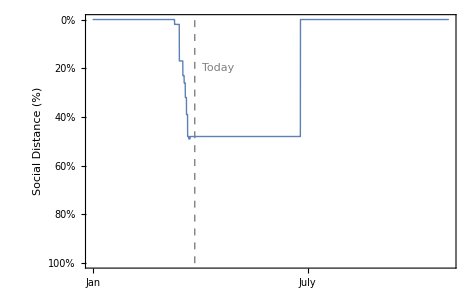

```mathematica
statePlots["NY","scenario1"]["Distancing"]
```

```mathematica
distancingStates={"CA","CO","CT","FL","GA","IL","IN","LA","MA","MI","NJ","NY","OH","OR","PA","SC","TX","VA","VT","WA","WI"};
```

Create PNG files of all the images for the website

```mathematica
Export["public/svg/state/"<>#<>"/scenario1/Distancing.svg",statePlots[#,"scenario1"]["Distancing"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario2/Distancing.svg",statePlots[#,"scenario2"]["Distancing"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario3/Distancing.svg",statePlots[#,"scenario3"]["Distancing"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario4/Distancing.svg",statePlots[#,"scenario4"]["Distancing"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario1/ICU.svg",statePlots[#,"scenario1"]["ICU"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario2/ICU.svg",statePlots[#,"scenario2"]["ICU"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario3/ICU.svg",statePlots[#,"scenario3"]["ICU"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario4/ICU.svg",statePlots[#,"scenario4"]["ICU"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario1/Deaths.svg",statePlots[#,"scenario1"]["Deaths"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario2/Deaths.svg",statePlots[#,"scenario2"]["Deaths"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario3/Deaths.svg",statePlots[#,"scenario3"]["Deaths"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario4/Deaths.svg",statePlots[#,"scenario4"]["Deaths"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario1/Progression.svg",statePlots[#,"scenario1"]["Progression"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario2/Progression.svg",statePlots[#,"scenario2"]["Progression"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario3/Progression.svg",statePlots[#,"scenario3"]["Progression"]]&/@distancingStates;
Export["public/svg/state/"<>#<>"/scenario4/Progression.svg",statePlots[#,"scenario4"]["Progression"]]&/@distancingStates;
Export["public/json/state/demographics.json",Association[(# -> statePlots[#, "scenario1"]["Demographics"]&)/@distancingStates]];
Export["public/json/state/"<>#<>"/summary.json",Association[{
"scenario1"->statePlots[#,"scenario1"]["Summary"],
"scenario2"->statePlots[#,"scenario2"]["Summary"],
"scenario3"->statePlots[#,"scenario3"]["Summary"],
"scenario4"->statePlots[#,"scenario4"]["Summary"]}]]&/@distancingStates;
```

```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"]
```

/Users/wbunting/Documents/Github/covidmodel